# Rigid-Body Mechanics from First Principles

#### Brian Beckman 29 Oct 2017

## Preliminaries

Some display rules to make the equations shorter and easier on the eyes. The following is an initialization cell.

Dependence on time t is denoted either in square brackets as in x[t] or with subscript as in x_t.

```mathematica
ClearAll[dpyRules];
dpyRules={Cos[a_[t_]]:>Subscript[c, Subscript[a, t]],Cos[n_ a_[t_]]:>Subscript[c, n Subscript[a, t]],
Sin[a_[t_]]:>Subscript[s, Subscript[a, t]],Sin[n_ a_[t_]]:>Subscript[s, n Subscript[a, t]],
Sec[a_[t_]]:>1/Subscript[c, Subscript[a, t]],Tan[a_[t_]]:>Subscript[tn, Subscript[a, t]],
Csc[a_[t_]]:>1/Subscript[s, Subscript[a, t]],Cot[a_[t_]]:>1/Subscript[tn, Subscript[a, t]],
a_''[t_]:>Subscript[ä, t],
a_'[t_]:>Subscript[ȧ, t],
a_[t_]:>Subscript[a, t]};

ClearAll[dpy];(*SetAttributes[dpy,Listable];*)
dpy[l_List]:=TraditionalForm[MatrixForm[Map[#/.dpyRules&,FullSimplify[l]]]];
dpy[x_]:=TraditionalForm[MatrixForm[FullSimplify[x]/.dpyRules]];

ClearAll[numRules];
numRules={g->1,c->1,m->1,d->1};

tmax=30;

ClearAll[cross];
cross[{a_,b_},{c_,d_}]:=a d-b c;

ClearAll[o,e1,e2,e3];o={0,0,0};{e1,e2,e3}=IdentityMatrix[3];
```

## Introduction

My best sources are Dare Wells’s Lagrangian Dynamics and Murray Spiegel’s Theoretical Mechanics. Many items are quoted directly from Wells, so I maintain his section numbering to facilitate cross reference, but this note is self-contained. I streamlined some notation, inserted my own foundational remarks, and emphasized certain points that are very common sources of error, even in published papers.

### Rotation and Mach’s Principle

Inertial rotation is measured, in an absolute sense, w.r.t. the distant galaxies (Mach’s Principle). Rotation of a reference frame and of a closed system makes no sense in an otherwise empty Universe. This is one of those odd facts of nature that, like quantum mechanics, defies deeper explanation. One can imagine a “fabric” of spacetime that allows us to detect rotation, but that is almost like the discredited electromagnetic aether and not a helpful concept. Perhaps, someday, Mach’s Principle will be reduced to quantum entanglement, a reduction that might be experimentally tested. For practical purposes, take Mach’s Principle as axiomatic. Mach’s Principle holds in general relativity and in quantum mechanics as well as in classical mechanics.

Physicists prefer to work in concise, coordinate-free mathematics as much as possible, but, in physics, unlike.7f mathematics, not all frames are created equal. Inertial frames are truly special; components of vector quantities measured in them are basic and foundational. Ultimately, kinematic vector quantities must be measured, component-wise, in orthogonal, locally Euclidean, inertial reference frames. This truth relates physics to the mathematics of differentiable manifolds.

In classical mechanics, angular velocities may be measured in frames that are merely non-rotating. Such frames may be non-inertial because they may be accelerating along straight lines. The measurement of angular velocity is not affected by translational motion in classical mechanics. In relativistic mechanics, angular.7f velocity.7f must be measured in a fully inertial frame because translation can skew, twist, and curve spacetime.

Mach's Principle implies that it is possible to establish a non-rotating frame and thus to measure angular velocity in an absolute sense w.r.t. this non-rotating frame. It is critical to distinguish the concept of measuring angular velocity in a non-rotating frame versus projecting the components of the vector into any frame, rotating or not. An angular velocity has components in any frame, rotating or not, but its components must be initially measured in a non-rotating frame.

### Sidebar: Relativity and Quantum Mechanics

In classical mechanics, inertial frames are absolute; mere addition of components suffices to transform translational velocities from one to another. We do these transformations almost without thinking because they're so intuitive. In relativistic mechanics, converting components measured in one inertial frame w.r.t. components measured in another inertial frame is more complicated and.7f non-intuitive. That's why Einsteinian relativity was so revolutionary: it required physicists to abandon cherished and “obvious” intuitions. Quantum mechanics was even worse. The combination of relativity and quantum mechanics results in a Universe that cannot be understood in intuitive ways, at least until the intuition is retrained to respect the truth. This retraining can take a lifetime, and the resulting, new intuitions are mathematical rather than physical because they do not relate to the ordinary experiences that our brains and minds evolved to expect.

### Physics Versus Mathematics

One difference between physics and mathematics is that physics is grounded in axioms about measurement, whereas mathematics is grounded in axioms about types and transformations. Physics uses mathematics once the measurements in inertial frames are made. The mathematics of classical mechanics can be aided by ordinary physical intuition, and this fact leads both to grand simplifications and to mistakes. The mathematics of relativity and quantum mechanics cannot be aided by ordinary physical intuitions, so simplifications are harder to find. As to mistakes, they abound in relativity and quantum mechanics, also, but are more often due to the much greater complexity of the mathematics.

## 8.2 Kinematics

8.2.A Angular Velocity as a Vector

-Graphics-

Fig. 8.1

Body rotating, but not translating, about point O of arbitrary, possibly non-inertial frame ℱ=^def{X,Y,Z}. O is a universal joint (three angular degrees of freedom). This situation, whereby O is at a fixed position in the body, is assumed and emphasized many times below. Assume angular velocity vector ω directed along OverVector[O a]. Let r be the position vector of particle m' in frame ℱ. The velocity of particle m' is

v=ω×r

or, in components

{v_X,v_Y,v_Z}=={ω_X,ω_Y,ω_Z}×{r_X,r_Y,r_Z}=={r_Z ω_Y-r_Y ω_Z,r_X ω_Z-r_Z ω_X,r_Y ω_X-r_X ω_Y}

Equation 2 above is equivalent to equation 8.1 on page 140 of Wells.

8.2.B Inertial Space Velocity

-Graphics-

Fig. 8-2

Goal: expression for inertial-space velocity of particle dm' in a non-inertial, body-pinned frame. m' is an arbitrary particle embedded in and fixed w.r.t. the rigid body.

The following definitions must be memorized. In particular, it is critical to remember that non-inertial means potentially rotating and translating in an arbitrary, time-varying fashion, and that non-rotating means potentially translating along straight lines, without continuous turning, in an arbitrary, time-varying fashion. A non-rotating frame may accelerate along a straight line in Euclidean space, and thus be non-inertial. A non-rotating frame may only change directions after coming to a full stop, in a way that will not turn a gyroscope in its gimbals.

ℱ=^def{X,Y,Z} 
NON-INERTIAL, BODY-PINNED 
frame rotating about O relative to body. The body may be rotating w.r.t. ℱ, but is not translating, i.e., it is fixed, w.r.t. O. Quoting Wells, loosely, “ℱ is NOT fastened to the body except at O.” If the body is not rotating w.r.t. ℱ --- the usual case --- ℱ is called BODY-FIXED.

ℱ'=^def{X',Y',Z'} 
NON-ROTATING, BODY-PINNED 
origin O, not inertially rotating, but possibly inertially translating. Wells considers only ℱ' frames that are axis-aligned with the inertial frame, but this is not necessary.

ℱ_1=^def{X_1,Y_1,Z_1} 
inertial, origin not necessarily at O

Let ω and u be the time-dependent angular velocity and linear velocity, respectively, of the body measured in the non-rotating, body-pinned frame ℱ'. The angular velocity would be the same as that measured in a fully inertial frame because ℱ' is not rotating.

The components of ω and u w.r.t. the non-rotating axes of ℱ' are as follows, where we change Wells' notation in an obvious way due to limitations of Mathematica's typesetting:

{(ω')_X,(ω')_Y,(ω')_Z}=^def{ω_X',ω_Y',ω_Z'}

{(u')_X,(u')_Y,(u')_Z}=^def{u_X',u_Y',u_Z'}

Let the time-dependent position components of the particle m', projected onto the body-pinned, non-rotating frame ℱ', be

r_m|ℱ'=^def{m_X',m_Y',m_Z'}

Prime notation doesn’t easily work in Mathematica because it means Derivative. Therefore, invoking equation 2, the components of ω, r, and u in ℱ' are

```mathematica
{uXPrime,uYPrime,uZPrime}->{ωXPrime,ωYPrime,ωZPrime}×{mXPrime,mYPrime,mZPrime}
```

{uXPrime,uYPrime,uZPrime}→{mZPrime ωYPrime-mYPrime ωZPrime,-mZPrime ωXPrime+mXPrime ωZPrime,mYPrime ωXPrime-mXPrime ωYPrime}

Projecting the non-rotating, body-pinned components of ω, r, and u back onto the non-inertial, body-pinned frame ℱ:

```mathematica
{Subscript[u, X],Subscript[u, Y],Subscript[u, Z]}->{Subscript[ω, X],Subscript[ω, Y],Subscript[ω, Z]}×{Subscript[m, X],Subscript[m, Y],Subscript[m, Z]}
```

{u_X,u_Y,u_Z}→{m_Z ω_Y-m_Y ω_Z,-m_Z ω_X+m_X ω_Z,m_Y ω_X-m_X ω_Y}

because the components of the cross product maintain the frame of its factor vectors (proof in Wells’s Appendix in terms of direction cosines; more elegant presentations entail Grassmann (Exterior) algebra and Clifford algebra).

The total (summed) inertial velocity of particle m' is the inertial velocity of O plus the velocity of m' measured in the non-rotating, body-pinned frame ℱ'. The inertial velocity of m', thus properly measured in the non-rotating frame, can be projected back into the non-inertial, body-pinned frame ℱ.

If O has inertial velocity v_O with components {v_OX,v_OY,v_OZ} w.r.t. the non-inertial, body-pinned frame ℱ, the total (summed) inertial velocity of particle m', projected onto the non-inertial, body-pinned frame ℱ is as follows:

{v_X,v_Y,v_Z}={v_OX,v_OY,v_OZ}+{ω_X,ω_Y,ω_Z}×{m_X,m_Y,m_Z}={m_Z ω_Y-m_Y ω_Z+v_OX,-m_Z ω_X+m_X ω_Z+v_OY,m_Y ω_X-m_X ω_Y+v_OZ}

In vector notation, this is

v_m=v_O+ω×r_m

or, using symbolic algebra

```mathematica
<<Notation`
```

```mathematica
Quiet[Symbolize[Subscript[v, O]];Symbolize[Subscript[v, m]];Symbolize[Subscript[r, m]];Symbolize[Subscript[v, OX]];Symbolize[Subscript[v, OY]];Symbolize[Subscript[v, OZ]];Symbolize[Subscript[Ω, X]];Symbolize[Subscript[Ω, Y]];Symbolize[Subscript[Ω, Z]];Symbolize[Subscript[ω, X]];Symbolize[Subscript[ω, Y]];Symbolize[Subscript[ω, Z]];Symbolize[Subscript[m, X]];Symbolize[Subscript[m, Y]];Symbolize[Subscript[m, Z]]];
```

```mathematica
With[{Subscript[v, O]={Subscript[v, OX],Subscript[v, OY],Subscript[v, OZ]},ω={Subscript[ω, X],Subscript[ω, Y],Subscript[ω, Z]},Subscript[r, m]={Subscript[m, X],Subscript[m, Y],Subscript[m, Z]}},
Subscript[v, O]+ω×Subscript[r, m]]
```

{v_OX+m_Z ω_Y-m_Y ω_Z,v_OY-m_Z ω_X+m_X ω_Z,v_OZ+m_Y ω_X-m_X ω_Y}

It’s extremely important to remember that ω and r_m are measured in the non-ROTATING, body-pinned frame ℱ'. This is emphasized in the stipulations below.

The summing is Galilean relativity, not true in special or general (Einsteinian) relativity.

8.2.C Stipulations

Loosely quoting Wells:

a. O must be attached to some point of the body.

b. ℱ may rotate about O with respect to the body. In practice, it is almost never chosen that way. In other words, ℱ is ALMOST always non-inertial, body-FIXED, not just body-pinned.

c. v_O must give components with respect to the instantaneous, time-dependent orientation of the non-inertial, body-pinned frame ℱ.

d. v_O is independent of the location of the particle m'. It is the inertial, time-dependent, translational velocity of the body point O. This is one reason that O must be fixed w.r.t. the body, i.e., attached in the language of paragraph a above.

e. The magnitude and direction of v_O depend on the instantaneous, time-dependent position of O. If O is not moving, then v_O is zero. But if the body has some other point P fixed in inertial space and O is not taken at this point, then v_O is not necessarily zero.

f. ω measured in an inertial frame is the same as ω measured in any non-rotating frame.

g. ω must give components with respect to the instantaneous, time-dependent orientation of the non-inertial, body-pinned frame ℱ.

h. ω may be translated anywhere so long as its direction remains constant. This does not obtain in general relativistic circumstances because arbitrary translation of vectors is not possible in curved spacetime.

i. v_O and ω are not constant in magnitude or direction, nor are their components in ℱ.

8.2.D Inertial Components

-Graphics-

Fig 8.3

The following definitions give preference to components in the non-inertial frame ℱ in the sense of avoiding.7f subscripts for components in that frame.

Let Ω_(1,ℱ) be the angular velocity of the non-inertial frame ℱ measured in the strictly inertial frame ℱ_1, with components projected back into ℱ:

Ω_(1,ℱ)|ℱ=^def{Ω_X,Ω_Y,Ω_Z}

As before, let v_(1,O) be the inertial velocity of point O with components {v_OX,v_OY,v_OZ} in the non-inertial frame ℱ:

v_(1,O)|ℱ=^def{v_OX,v_OY,v_OZ}

Let a certain free particle m, not necessarily part of any rigid body, have time-dependent inertial coordinates r_1=^def{x_1,y_1,z_1}, projected back into the non-inertial frame ℱ:

r_1|ℱ=^def{x,y,z}

Let the inertial velocity of particle m be v_(1,m) have components {v_X,v_Y,v_Z} in the non-inertial frame ℱ:

v_(1,m)|ℱ=^def{v_X,v_Y,v_Z}

First, let m be fixed w.r.t. ℱ, meaning its components measured in that frame are constant. By equation 7:

{v_X,v_Y,v_Z}={v_OX,v_OY,v_OZ}+{Ω_X,Ω_Y,Ω_Z}×{x,y,z}

In vector notation

v=v_O+Ω×r

To emphasize: The quantities v_O and Ω are measured in an inertial frame, then their components are projected back into a non-inertial frame.

Now let particle m move w.r.t. the non-inertial frame ℱ, meaning that its components measured in that frame {x,y,z} are time-dependent, that is, functions of time. Let their derivatives be {ẋ,ẏ,ż}. Invoke Galilean relativity, which obtains in all frames for linear velocities, and just add those relative velocities component-wise:

{v_X,v_Y,v_Z}={v_OX,v_OY,v_OZ}+{ẋ,ẏ,ż}+{Ω_X,Ω_Y,Ω_Z}×{x,y,z}

or

v=v_O+ṙ+Ω×r

A more rigorous proof awaits Euler angles. Alternatively, and not presented here, quaternions furnish a proof. Quaternions avoid certain singularities with Euler angles and are more concise, algebraically.

## 8.3 Kinetics

The numerical value of kinetic energy obviously depends on the frame of reference. A particle at rest in frame ℱ has no kinetic energy. The same particle in a moving frame has non-zero kinetic energy. A stationary cannonball will deliver kinetic energy when a moving train (frame) slams into it, just as if the cannonball were fired into a stationary train at the same speed.

Newton’s laws obtain only w.r.t. quantities measured in inertial frames. However, those quantities may be expressed in non-inertial frames and the laws still hold. We can derive equations of motion in terms of convenient, Lagrangian coordinates using the kinetic energy expressed in these coordinates, even though the numerical value of this kinetic energy will not be the same as the numerical value of the kinetic energy measured in the inertial frame. This fact enables us to greatly simplify complex problems.

The kinetic energy of a general rigid body, with all components of inertial quantities measured in inertial frames and projected back onto an arbitrary non-inertial frame, is found by integrating (or summing) equation 12 over all particles in the rigid body. For each particle, equation 12 expands and collects as follows:

```mathematica
With[{Subscript[v, O]={Subscript[v, OX],Subscript[v, OY],Subscript[v, OZ]},Ω={Subscript[Ω, X],Subscript[Ω, Y],Subscript[Ω, Z]},r={x,y,z}},
With[{v=Subscript[v, O]+Ω×r},
1/2 m v.v//Expand//Collect[#,Ω]&]]
```

(m v_OX^2)/2+(m v_OY^2)/2+(m v_OZ^2)/2+((m y^2)/2+(m z^2)/2) Ω_X^2+((m x^2)/2+(m z^2)/2) Ω_Y^2+(m v_OY x-m v_OX y) Ω_Z+((m x^2)/2+(m y^2)/2) Ω_Z^2+Ω_X (m v_OZ y-m v_OY z-m x y Ω_Y-m x z Ω_Z)+Ω_Y (-m v_OZ x+m v_OX z-m y z Ω_Z)

### Identification of Subexpressions

Recognizing the terms quadratic in components of Ω as “dyadic” products of Ω with the moment of inertia, and recognizing quadratic terms in v_OX, v_OY, and v_OZ as the translational kinetic energy of the rigid body because O is fixed in the rigid body (that’s the reason we keep emphasizing this stipulation 8.2.C.a)

```mathematica
With[{Subscript[v, O]={Subscript[v, OX],Subscript[v, OY],Subscript[v, OZ]},Ω={Subscript[Ω, X],Subscript[Ω, Y],Subscript[Ω, Z]},r={x,y,z}},
With[{v=Subscript[v, O]+Ω×r,
offDiagonalΩIΩTerms=
-2m x y Subscript[Ω, X] Subscript[Ω, Y]-2m y z Subscript[Ω, Y] Subscript[Ω, Z]-2m z x Subscript[Ω, Z] Subscript[Ω, X],
diagonalΩIΩTerms=
(m y^2+m z^2) Subscript[Ω, X]^2+(m x^2+m z^2) Subscript[Ω, Y]^2+(m x^2+m y^2) Subscript[Ω, Z]^2},
With[{ΩIΩ=offDiagonalΩIΩTerms+diagonalΩIΩTerms},
Collect[Expand[
1/2 m v.v-1/2 ΩIΩ-1/2 m Subscript[v, O].Subscript[v, O]],
Ω]]]]
```

(m v_OZ y-m v_OY z) Ω_X+(-m v_OZ x+m v_OX z) Ω_Y+(m v_OY x-m v_OX y) Ω_Z

We recognize the remaining term as a dot and cross product:

```mathematica
With[{Subscript[v, O]={Subscript[v, OX],Subscript[v, OY],Subscript[v, OZ]},Ω={Subscript[Ω, X],Subscript[Ω, Y],Subscript[Ω, Z]},r={x,y,z}},
With[{v=Subscript[v, O]+Ω×r,
offDiagonalΩIΩTerms=
-2m x y Subscript[Ω, X] Subscript[Ω, Y]-2m y z Subscript[Ω, Y] Subscript[Ω, Z]-2m z x Subscript[Ω, Z] Subscript[Ω, X],
diagonalΩIΩTerms=
(m y^2+m z^2) Subscript[Ω, X]^2+(m x^2+m z^2) Subscript[Ω, Y]^2+(m x^2+m y^2) Subscript[Ω, Z]^2},
With[{ΩIΩ=offDiagonalΩIΩTerms+diagonalΩIΩTerms},Expand[1/2 m v.v==1/2 m Subscript[v, O].Subscript[v, O]+1/2 ΩIΩ+m Subscript[v, O].Ω×r]]]]
```

True

Summing over all masses

reduces r to the time-dependent position of the center of mass with respect to O (fixed in the body), r_CM

replaces the time-dependent particle moment of inertia above with the time-dependent body moment of inertia about O (fixed in the body), not necessarily the center of mass

Remember, the velocities and angular velocities are measured in inertial space and projected back into the non-inertial frame ℱ.

in traditional vector notation, this is

1/2 M v • v=1/2 M v_O• v_O+1/2 Ω • I • Ω+M v_O• Ω×r_CM

## 8.4 Summary and Emphasis

a. Ω and v_O must be measured in inertial space and their components projected onto any convenient frame.

b. O must not translate w.r.t. the body.

c. r_CM and I will not, in general, be constant in arbitrary, O-attached frames.

d. In body-fixed frames, r_CM and I are constant. This fact leads to grand simplifications and is the reason body-fixed frames are almost always employed.

e. In body-centered, body-fixed frames, r_CM is zero. In body-centered, body-fixed, principal-axis frames, the off-diagonal components of the moment of inertia vanish. This results in the following, much simpler form for the kinetic energy

1/2 M v • v=1/2 M v_O• v_O+1/2(Ω_X^2 I_XX+Ω_Y^2 I_YY+Ω_Z^2 I_ZZ)

The second term has the form of a dot product of a (formal-only) vector of squared components of Ω with a (formal-only) vector of the diagonal components of I. These formal vectors are mathematical conveniences and have no direct physical interpretation, that is, w.r.t. to measurement axioms.

## 2D Cart and Baton

Lagrangian

Kinetic energy of the baton is due to

linear motion of its CM, located at bat. This location is fixed w.r.t. the baton, so it qualifies as the origin O of non-inertial frame ℱ.

rotational motion about its CM. Take ℱ to be the principal-axis frame, so the moment of inertia is constant in this frame.

We present two Lagrangians: one just for the baton, the second based for the baton-cart system.7f.7f. The second Lagrangian was used in Moylan’s second article. The two Lagrangians produce the same results.

### Baton Only

Restrict attention to the baton. Include only its kinetic energy in the Lagrangian. The generalized force on the cart is f[t]. Some of that force is absorbed in momentum changes in the cart, namely c x''[t]. Subtract that absorbed force to produce the net generalized force on the baton tip, which rests on the cart.

```mathematica
ClearAll[
x(*position of cart and baton bottom*),
θ(*elevation angle*),
m(*mass of baton*),
c(*mass of cart*),
d(*length of baton*),
t,Lcrds,Lvels,cart,bat,cm,Jbat,Jcm,Tlin,Trot,V,L,F,zCrossBat,Leqns,peqns]
Lcrds={x[t],θ[t]};(*measured in inertial frame*)
Lvels=D[Lcrds,t];(*symbolic derivatives*)
cart={x[t],0};(*vectors in curly braces*)
bat=cart+d/2{Cos[θ[t]],Sin[θ[t]]};
Jbat=(1/12 m d^2);
Tlin=With[{v=D[bat,t]},1/2 m v.v];
Trot=1/2 Jbat θ'[t]^2;(*about baton cm, not system cm*)
V=g m bat⟦2⟧;
L=Tlin+Trot-V;
F={f[t]-c x''[t],0};(*some force absorbed by momentum change in the cart*)
(Leqns=MapThread[
{q,v,h}↦D[D[L,v],t]-D[L,q]==h,
{Lcrds(*qs*),Lvels(*vs*),F(*hs*)}]);
(peqns=Leqns)//dpy
```

(d m (θ̇)_t^2 c_θ_t+d m s_θ_t (θ̈)_t+2 f_t==2 (c+m) (ẍ)_t
d m (3 g c_θ_t+2 d (θ̈)_t-3 s_θ_t (ẍ)_t)==0)

TODO: check against fixed-pivot pendulum, non-linear solution.

### Baton Plus Cart

Include the cart kinetic energy. Each of the cart and the baton is resolved in its own BODY-FIXED, CENTER-OF-MASS, PRINCIPAL-AXIS frame. The cart does not rotate about its center of mass, thus there is no rotational kinetic energy for the cart. Use the total applied force f[t] as the generalized force term in the Lagrangian.

```mathematica
Tlin=1/2 c x'[t]^2+With[{v=D[bat,t]},1/2 m v.v];
V=g m bat⟦2⟧;
L=Tlin+Trot-V;
(Leqns=MapThread[
{q,v,h}↦D[D[L,v],t]-D[L,q]==h,
{Lcrds(*qs*),Lvels(*vs*),{f[t],0}(*hs*)}]);
(peqns=Leqns/.numRules)//dpy
```

((θ̇)_t^2 c_θ_t+2 f_t+s_θ_t (θ̈)_t==4 (ẍ)_t
3 c_θ_t+2 (θ̈)_t==3 s_θ_t (ẍ)_t)

These equations agree with Moylan’ s corrected second article. His first article had at least two mistakes.

```mathematica
inits2D={x[0]==0,θ[0]==π/2-1°,x'[0]==0,θ'[0]==0};
psoln=NDSolve[Join[peqns/.{f[t]->0},inits2D],{x[t],θ[t]},{t,0,tmax}]
```

{{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

Newtonian

Considering just the forces and torques on the baton,

```mathematica
ClearAll[neqns];
(neqns=
With[{e1={1,0},e2={0,1}},
With[{maX=m*D[bat⟦1⟧,{t,2}],maY=m D[bat⟦2⟧,{t,2}]},
With[{torqueBatcm=
With[{r=bat-cart},
-cross[r,m g e2]+cross[r,f[t] e1]]},
With[{},
{maX==f[t],
torqueBatcm==Jbat*θ''[t](*torque*)}]]]]
/.numRules)//dpy
```

((θ̇)_t^2 c_θ_t+2 f_t+s_θ_t (θ̈)_t==2 (ẍ)_t
6 c_θ_t+6 f_t s_θ_t+(θ̈)_t==0)

```mathematica
nsoln=NDSolve[Join[neqns/.{f[t]->0},inits2D],{x[t],θ[t]},{t,0,tmax}]
```

{{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

Plotting and Animation

```mathematica
AnimatePendulum[soln_]:=
(Animate[
Evaluate[
DrawSinglePendulum[x[t]/.soln,{θ[t]/.soln,1,1},t]],
{t,0,Max[First[x/.soln]]},
DefaultDuration->15,AnimationRunning->False]);
```

```mathematica
ClearAll[DrawSinglePendulum];
DrawSinglePendulum[cart_,{angle1_,length1_,mass1_},t_]:=
Module[{width1,density=30},
width1=mass1/length1/density;
Graphics[
{{Blue,Rectangle[{cart-1/4,-1/15},{cart+1/4,1/15}]},
{Orange,
Translate[
Rotate[
Rectangle[{0,width1},{length1,-width1}],
angle1,{0,0}],
{cart,0}]}   },
PlotRange->2,ImageSize->280,
Frame->True,Axes->True,AxesStyle->Dashed,
PlotLabel->"t"==NumberForm[t,{4,2}]   ]   ]
```

```mathematica
ClearAll[SimulatePendulum];
SimulatePendulum[eqns_,inits_,force_]:=
AnimatePendulum[
First[
NDSolve[
Join[eqns/.f[t]->force,inits],
{x,θ},
{t,0,tmax}]]]
```

```mathematica
SimulatePendulum[peqns,inits2D,{0,0,0}]
```

```mathematica
verybumpy[t_]=Sum[RandomReal[{-10,10}]Exp[-10(t-RandomInteger[15])^2],{20}]
```

-7.06623 ⅇ^(-10 (-14+t)^2)-7.48104 ⅇ^(-10 (-13+t)^2)+2.18786 ⅇ^(-10 (-12+t)^2)+2.27415 ⅇ^(-10 (-11+t)^2)+3.21237 ⅇ^(-10 (-10+t)^2)-23.1741 ⅇ^(-10 (-7+t)^2)+8.52924 ⅇ^(-10 (-6+t)^2)-7.85926 ⅇ^(-10 (-4+t)^2)+2.55835 ⅇ^(-10 (-2+t)^2)+8.36141 ⅇ^(-10 (-1+t)^2)

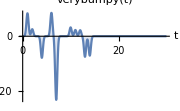

```mathematica
Plot[verybumpy[t],{t,0,30},
PlotRange->All,
Filling->Axis,
PlotLabel->HoldForm[verybumpy[t]],AxesLabel->{t}]
```

Check plausibility with a sinusoidal force:

```mathematica
SimulatePendulum[0.1Sin[2π t/10],0]
```